```mathematica
input = Import[NotebookDirectory[]<>"nbs.txt", "Table"];
ppt = 1000;
min = Min[Flatten[input]];
max = Max[Flatten[input]];
ListAnimate[Table[ListPointPlot3D[{input⟦i⟧⟦1;;3⟧, input⟦i⟧⟦4;;6⟧, input⟦i⟧⟦7;;9⟧},PlotRange-> {{min,max}, {min, max}, {min, max}}], {i, 1, 1000}]]
```

```mathematica
input = Import[NotebookDirectory[]<>"nbs.txt", "Table"];
ppt = 1000;
min = Min[Flatten[input]];
max = Max[Flatten[input]];
ListAnimate[Table[ListPointPlot3D[{input⟦3(i-1)+1;;3i⟧},PlotRange-> {{min,max}, {min, max}, {min, max}}], {i, 1, 1000}]]
```

```mathematica
ListPointPlot3D[input⟦1;;3⟧, PlotRange->All]
```

-Graphics3D-

```mathematica
input⟦1;;100⟧
```

{{0.918375,-0.911295,-0.358648},{0.054231,-2.1391,0.028043},{1.66908,0.056309,1.11968},{0.91851,-0.911079,-0.359147},{0.053884,-2.13958,0.028076},{1.66927,0.056569,1.11995},{0.918907,-0.910444,-0.360616},{0.052864,-2.14101,0.028171},{1.66985,0.057332,1.12076},{0.919565,-0.909393,-0.363052},{0.051173,-2.14338,0.028329},{1.67081,0.058597,1.12209},{0.920481,-0.907928,-0.366454},{0.048815,-2.14669,0.028549},{1.67215,0.060362,1.12396},{0.921652,-0.906054,-0.370818},{0.045794,-2.15092,0.028833},{1.67386,0.062626,1.12635},{0.923075,-0.903777,-0.376141},{0.042116,-2.15608,0.029179},{1.67595,0.065383,1.12927},{0.924744,-0.901103,-0.382418},{0.037789,-2.16214,0.029589},{1.67841,0.06863,1.13271},{0.926655,-0.89804,-0.389642},{0.032822,-2.1691,0.030062},{1.68124,0.072362,1.13666},{0.928802,-0.894597,-0.397807},{0.027223,-2.17695,0.030597},{1.68443,0.076574,1.14113},{0.931178,-0.890783,-0.406906},{0.021004,-2.18567,0.031196},{1.68798,0.081259,1.14611},{0.933776,-0.886607,-0.41693},{0.014175,-2.19524,0.031857},{1.69188,0.086412,1.1516},{0.93659,-0.882081,-0.427871},{0.006749,-2.20565,0.032582},{1.69614,0.092023,1.15758},{0.939612,-0.877215,-0.439717},{-0.001262,-2.21688,0.033369},{1.70073,0.098087,1.16406},{0.942834,-0.872019,-0.452459},{-0.009844,-2.22891,0.034218},{1.70566,0.104594,1.17103},{0.946249,-0.866507,-0.466085},{-0.018983,-2.24172,0.03513},{1.71093,0.111536,1.17847},{0.94985,-0.860688,-0.480584},{-0.028666,-2.25529,0.036104},{1.71651,0.118905,1.18639},{0.953627,-0.854575,-0.495941},{-0.038879,-2.26961,0.037139},{1.72241,0.12669,1.19478},{0.957575,-0.848178,-0.512145},{-0.049606,-2.28465,0.038235},{1.72863,0.134884,1.20363},{0.961685,-0.841509,-0.52918},{-0.060834,-2.30039,0.039391},{1.73514,0.143476,1.21292},{0.96595,-0.834579,-0.547034},{-0.072547,-2.31682,0.040606},{1.74196,0.152456,1.22266},{0.970363,-0.827398,-0.56569},{-0.084731,-2.3339,0.041881},{1.74906,0.161814,1.23284},{0.974918,-0.819977,-0.585134},{-0.097373,-2.35162,0.043214},{1.75644,0.171542,1.24344},{0.979607,-0.812326,-0.60535},{-0.110457,-2.36997,0.044603},{1.76409,0.181628,1.25445},{0.984424,-0.804454,-0.626322},{-0.123969,-2.38892,0.04605},{1.77201,0.192063,1.26588},{0.989364,-0.796371,-0.648035},{-0.137896,-2.40845,0.047551},{1.78019,0.202838,1.27771},{0.99442,-0.788086,-0.670472},{-0.152224,-2.42854,0.049107},{1.78862,0.213941,1.28992},{0.999587,-0.779608,-0.693617},{-0.166941,-2.44918,0.050716},{1.79729,0.225364,1.30252},{1.00486,-0.770944,-0.717453},{-0.182032,-2.47034,0.052377},{1.8062,0.237097,1.3155},{1.01023,-0.762102,-0.741965},{-0.197486,-2.49202,0.054089},{1.81534,0.249131,1.32883},{1.0157,-0.753091,-0.767135},{-0.213291,-2.51418,0.055851},{1.8247,0.261457,1.34253},{1.02127,-0.743916,-0.792947},{-0.229433,-2.53682,0.057662},{1.83428,0.274064,1.35656},{1.02691,-0.734584,-0.819385},{-0.245903,-2.55992,0.059521},{1.84406,0.286945,1.37094},{1.03265,-0.725103,-0.846433}}

```mathematica
ListAnimate[Table[ListPlot[input⟦160*i;;160*(i+1)⟧ ],{i, 1, 999}]]
```

```mathematica
input
```

{{0.050818,-1.79898},{-0.972452,0.148493},{-3.43216,3.16391},{-3.71883,1.70405},{-1.57348,2.05821},{-0.018028,-0.499105},159988,{0.087182,3.91734},{-0.92576,-0.183621},{-0.757751,-1.40662},{2.95169,1.37848},{2.08997,-0.148088},{0.580845,1.21062}}
 |  |  |  |

-Graphics3D-

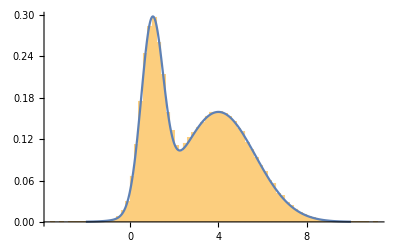

-Graphics3D-

C:\Users\Haik\Desktop\nbodyVIS\data.txt

```mathematica
boxsize=5;
velmax=1000;
mmax=1000;
nparticles=1000;
masses=RandomReal[{0,mmax},nparticles];
xpos=RandomReal[{-boxsize,boxsize},nparticles];
ypos=RandomReal[{-boxsize,boxsize},nparticles];
zpos=RandomReal[{-boxsize,boxsize},nparticles];
xvel=RandomReal[{-velmax,velmax},nparticles];
yvel=RandomReal[{-velmax,velmax},nparticles];
zvel=RandomReal[{-velmax,velmax},nparticles];

all=Table[{masses[[i]],xpos[[i]],ypos[[i]],zpos[[i]],xvel[[i]],yvel[[i]],zvel[[i]]},{i,nparticles}];

ListPointPlot3D[Table[{xpos[[i]],ypos[[i]],zpos[[i]]},{i,nparticles}],PlotRange->All]


dist=MixtureDistribution[{1,2},{NormalDistribution[1,1/2],NormalDistribution[4,5/3]}];
data=RandomVariate[dist,10^5];
Show[Histogram[data,45,"ProbabilityDensity"],Plot[PDF[dist,x],{x,-2,10},PlotStyle->PointSize[Medium]]]


pos=RandomVariate[MultinormalDistribution[{0,0,0},{{1,0,0},{0,1,0},{0,0,1}}],nparticles];

ListPointPlot3D[pos,PlotRange->All]
Export[NotebookDirectory[]<>"data.txt",pos]
```

```mathematica
npart =27;
Export[NotebookDirectory[]<>"grid.dat",Tuples[Table[i, {i, 0, 4, 2}],3], "Table"]
```

C:\Users\Haik\Desktop\nbodyVIS\grid.dat

```mathematica
Tuples
```